# Въведение

```mathematica
6+7
```

13

пояснение за работа със списъци:

```mathematica
vec = {4,5,{1/2,5^2},ⅇ,ArcSin[23.89]}
```

{4,5,{1/2,25},ⅇ,1.5708-3.86617 ⅈ}

```mathematica
vec1 = {4,5,{1/2,5^2},ⅇ,ArcSin[23.89]};
```

```mathematica
vec1
```

{4,5,{1/2,25},ⅇ,1.5708-3.86617 ⅈ}

```mathematica
vec^2
```

{16,25,{1/4,625},ⅇ^2,-12.4799-12.1459 ⅈ}

```mathematica
Tan[vec]
```

{Tan[4],Tan[5],{Tan[1/2],Tan[25]},Tan[ⅇ],1.07476×10^-19-1.00088 ⅈ}

```mathematica
%//N
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
vec2 = {4.0,5.,{1./2,5.^2},ⅇ//N,ArcSin[23.89]};
Tan[vec2]
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
1.1578212823495777
```

начин за изписване на функции

```mathematica
Tan@vec2
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
vec2//Tan
```

{1.15782,-3.38052,{0.546302,-0.133526},-0.45055,1.07476×10^-19-1.00088 ⅈ}

```mathematica
N[ⅇ]
```

2.71828

```mathematica
N[ⅇ,20]
```

2.7182818284590452354

```mathematica
N[ⅇ,200](* неперовото число с 200 значещи цифри *)
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427427466391932003059921817413596629043572900334295260595630738132328627943490763233829880753195251019

# КЧМ за решаване на нелинейни уравнения

Задача: Дадено е уравнението:
x^5+103 sin x -34 x^3 - 23 = 0
1. Да се визуализира функцията и да се определят броя на корените.
2. Да се локализира един от корените.
3. Уточнете локализирания корен  по метода на разполовяването.
4. Оценка на грешката
5.Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването използвайки интервала от локализацията на корена?

```mathematica
f[x_]:= x^5+103 Sin[x]-34 x^3-23
```

```mathematica
f[x]
```

-23-34 x^3+x^5+103 Sin[x]

## 1. Да се визуализира функцията и да се определят броя на корените.

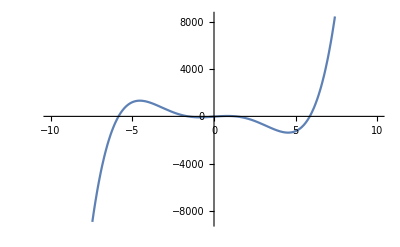

```mathematica
Plot[f[x],{x,-10,10}]
```

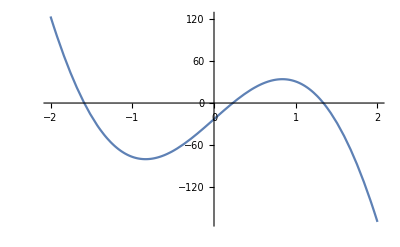

```mathematica
Plot[f[x],{x,-2,2}]
```

## 2. Да се локализира един от корените.

Локализираме най-малкия корен

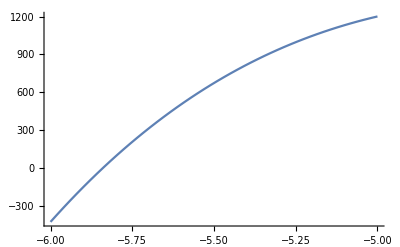

```mathematica
Plot[f[x],{x,-6,-5}]
```

```mathematica
f[-6.]
```

-426.22

```mathematica
f[-5.]
```

1200.77

Извод: 
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(-6) = -426.22... < 0
      f(-5) = 1200.77.... >0
      => Функцията има различни знаци в двата края на разглеждания интервал [-6; -5].
      От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-6; -5].

## 3. Уточнете локализирания корен по метода на разполовяването.

### уточнение за цикли и основни преходи

```mathematica
For[i = 0, i < 4,i++,Print[i]]
```

0

1

2

3

```mathematica
i
```

4

```mathematica
If[i < 2,Print["малко"],Print["голямо"]]
```

голямо

```mathematica
For[i = 0, i < 4,i++,
(*тяло на цикъла*)
Print[i];
If[i < 2,Print["малко"],Print["голямо"]]
]
```

0

малко

1

малко

2

голямо

3

голямо

### Съставяне на програмен код, реализиращ метода на разполовяването

основен код

```mathematica
f[x_]:= x^5+103 Sin[x]-34 x^3-23
 a = -6.; b = -5.;
For[n = 0,n <= 3,n++,
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2
," f(m_n)=  ",f[m],"ε_n = ", (b-a)/2];
If[f[m]> 0,b = m, a = m]
]
```

n = 0 a_n = -6. b_n = -5. m_n = -5.5 f(m_n)=  673.577ε_n = 0.5

n = 1 a_n = -6. b_n = -5.5 m_n = -5.75 f(m_n)=  207.58ε_n = 0.25

n = 2 a_n = -6. b_n = -5.75 m_n = -5.875 f(m_n)=  -86.6728ε_n = 0.125

n = 3 a_n = -5.875 b_n = -5.75 m_n = -5.8125 f(m_n)=  65.9004ε_n = 0.0625

```mathematica
f[-5.5]
```

673.577

Извод: На третата стъпка сме получили приближено решение -5.81 с точност 0.0625
пускаме с повече итерации:

```mathematica
f[x_]:= x^5+103 Sin[x]-34 x^3-23
 a = -6.; b = -5.;
For[n = 0,n <= 27,n++,
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2
," f(m_n)=  ",f[m],"ε_n = ", (b-a)/2];
If[f[m]> 0,b = m, a = m]
]
```

n = 0 a_n = -6. b_n = -5. m_n = -5.5 f(m_n)=  673.577ε_n = 0.5

n = 1 a_n = -6. b_n = -5.5 m_n = -5.75 f(m_n)=  207.58ε_n = 0.25

n = 2 a_n = -6. b_n = -5.75 m_n = -5.875 f(m_n)=  -86.6728ε_n = 0.125

n = 3 a_n = -5.875 b_n = -5.75 m_n = -5.8125 f(m_n)=  65.9004ε_n = 0.0625

n = 4 a_n = -5.875 b_n = -5.8125 m_n = -5.84375 f(m_n)=  -8.99803ε_n = 0.03125

n = 5 a_n = -5.84375 b_n = -5.8125 m_n = -5.82813 f(m_n)=  28.7949ε_n = 0.015625

n = 6 a_n = -5.84375 b_n = -5.82813 m_n = -5.83594 f(m_n)=  9.98477ε_n = 0.0078125

n = 7 a_n = -5.84375 b_n = -5.83594 m_n = -5.83984 f(m_n)=  0.515009ε_n = 0.00390625

n = 8 a_n = -5.84375 b_n = -5.83984 m_n = -5.8418 f(m_n)=  -4.2361ε_n = 0.00195313

n = 9 a_n = -5.8418 b_n = -5.83984 m_n = -5.84082 f(m_n)=  -1.85919ε_n = 0.000976563

n = 10 a_n = -5.84082 b_n = -5.83984 m_n = -5.84033 f(m_n)=  -0.671752ε_n = 0.000488281

n = 11 a_n = -5.84033 b_n = -5.83984 m_n = -5.84009 f(m_n)=  -0.0782872ε_n = 0.000244141

n = 12 a_n = -5.84009 b_n = -5.83984 m_n = -5.83997 f(m_n)=  0.218382ε_n = 0.00012207

n = 13 a_n = -5.84009 b_n = -5.83997 m_n = -5.84003 f(m_n)=  0.0700526ε_n = 0.0000610352

n = 14 a_n = -5.84009 b_n = -5.84003 m_n = -5.84006 f(m_n)=  -0.00411599ε_n = 0.0000305176

n = 15 a_n = -5.84006 b_n = -5.84003 m_n = -5.84004 f(m_n)=  0.0329687ε_n = 0.0000152588

n = 16 a_n = -5.84006 b_n = -5.84004 m_n = -5.84005 f(m_n)=  0.0144264ε_n = 7.62939×10^-6

n = 17 a_n = -5.84006 b_n = -5.84005 m_n = -5.84005 f(m_n)=  0.00515523ε_n = 3.8147×10^-6

n = 18 a_n = -5.84006 b_n = -5.84005 m_n = -5.84006 f(m_n)=  0.000519628ε_n = 1.90735×10^-6

n = 19 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  -0.00179818ε_n = 9.53674×10^-7

n = 20 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  -0.000639275ε_n = 4.76837×10^-7

n = 21 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  -0.0000598237ε_n = 2.38419×10^-7

n = 22 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  0.000229902ε_n = 1.19209×10^-7

n = 23 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  0.0000850391ε_n = 5.96046×10^-8

n = 24 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  0.0000126077ε_n = 2.98023×10^-8

n = 25 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  -0.000023608ε_n = 1.49012×10^-8

n = 26 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  -5.50016×10^-6ε_n = 7.45058×10^-9

n = 27 a_n = -5.84006 b_n = -5.84006 m_n = -5.84006 f(m_n)=  3.55377×10^-6ε_n = 3.72529×10^-9

```mathematica
f[x_]:= x^5+103 Sin[x]-34 x^3-23
 a = -6.; b = -5.;
For[n = 0,n <= 27,n++,
Print["n = ",n," a_n = ",SetPrecision[a,15]," b_n = ",SetPrecision[b,15]," m_n = ",SetPrecision[m = (a+b)/2,15]
," f(m_n)=  ",f[m],"ε_n = ", (b-a)/2];
If[f[m]> 0,b = m, a = m]
]
```

n = 0 a_n = -6. b_n = -5. m_n = -5.5 f(m_n)=  673.577ε_n = 0.5

n = 1 a_n = -6. b_n = -5.5 m_n = -5.75 f(m_n)=  207.58ε_n = 0.25

n = 2 a_n = -6. b_n = -5.75 m_n = -5.875 f(m_n)=  -86.6728ε_n = 0.125

n = 3 a_n = -5.875 b_n = -5.75 m_n = -5.8125 f(m_n)=  65.9004ε_n = 0.0625

n = 4 a_n = -5.875 b_n = -5.8125 m_n = -5.84375 f(m_n)=  -8.99803ε_n = 0.03125

n = 5 a_n = -5.84375 b_n = -5.8125 m_n = -5.828125 f(m_n)=  28.7949ε_n = 0.015625

n = 6 a_n = -5.84375 b_n = -5.828125 m_n = -5.8359375 f(m_n)=  9.98477ε_n = 0.0078125

n = 7 a_n = -5.84375 b_n = -5.8359375 m_n = -5.83984375 f(m_n)=  0.515009ε_n = 0.00390625

n = 8 a_n = -5.84375 b_n = -5.83984375 m_n = -5.841796875 f(m_n)=  -4.2361ε_n = 0.00195313

n = 9 a_n = -5.841796875 b_n = -5.83984375 m_n = -5.8408203125 f(m_n)=  -1.85919ε_n = 0.000976563

n = 10 a_n = -5.8408203125 b_n = -5.83984375 m_n = -5.84033203125 f(m_n)=  -0.671752ε_n = 0.000488281

n = 11 a_n = -5.84033203125 b_n = -5.83984375 m_n = -5.840087890625 f(m_n)=  -0.0782872ε_n = 0.000244141

n = 12 a_n = -5.840087890625 b_n = -5.83984375 m_n = -5.8399658203125 f(m_n)=  0.218382ε_n = 0.00012207

n = 13 a_n = -5.840087890625 b_n = -5.8399658203125 m_n = -5.84002685546875 f(m_n)=  0.0700526ε_n = 0.0000610352

n = 14 a_n = -5.840087890625 b_n = -5.84002685546875 m_n = -5.84005737304688 f(m_n)=  -0.00411599ε_n = 0.0000305176

n = 15 a_n = -5.84005737304688 b_n = -5.84002685546875 m_n = -5.84004211425781 f(m_n)=  0.0329687ε_n = 0.0000152588

n = 16 a_n = -5.84005737304688 b_n = -5.84004211425781 m_n = -5.84004974365234 f(m_n)=  0.0144264ε_n = 7.62939×10^-6

n = 17 a_n = -5.84005737304688 b_n = -5.84004974365234 m_n = -5.84005355834961 f(m_n)=  0.00515523ε_n = 3.8147×10^-6

n = 18 a_n = -5.84005737304688 b_n = -5.84005355834961 m_n = -5.84005546569824 f(m_n)=  0.000519628ε_n = 1.90735×10^-6

n = 19 a_n = -5.84005737304688 b_n = -5.84005546569824 m_n = -5.84005641937256 f(m_n)=  -0.00179818ε_n = 9.53674×10^-7

n = 20 a_n = -5.84005641937256 b_n = -5.84005546569824 m_n = -5.8400559425354 f(m_n)=  -0.000639275ε_n = 4.76837×10^-7

n = 21 a_n = -5.8400559425354 b_n = -5.84005546569824 m_n = -5.84005570411682 f(m_n)=  -0.0000598237ε_n = 2.38419×10^-7

n = 22 a_n = -5.84005570411682 b_n = -5.84005546569824 m_n = -5.84005558490753 f(m_n)=  0.000229902ε_n = 1.19209×10^-7

n = 23 a_n = -5.84005570411682 b_n = -5.84005558490753 m_n = -5.84005564451218 f(m_n)=  0.0000850391ε_n = 5.96046×10^-8

n = 24 a_n = -5.84005570411682 b_n = -5.84005564451218 m_n = -5.8400556743145 f(m_n)=  0.0000126077ε_n = 2.98023×10^-8

n = 25 a_n = -5.84005570411682 b_n = -5.8400556743145 m_n = -5.84005568921566 f(m_n)=  -0.000023608ε_n = 1.49012×10^-8

n = 26 a_n = -5.84005568921566 b_n = -5.8400556743145 m_n = -5.84005568176508 f(m_n)=  -5.50016×10^-6ε_n = 7.45058×10^-9

n = 27 a_n = -5.84005568176508 b_n = -5.8400556743145 m_n = -5.84005567803979 f(m_n)=  3.55377×10^-6ε_n = 3.72529×10^-9

```mathematica
f[x_]:= x^5+103 Sin[x]-34 x^3-23
 a = -6.; b = -5.;
epszad = 0.0001;
eps = Infinity;
For[n = 0,eps > epszad,n++,
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2
," f(m_n)=  ",f[m],"ε_n = ", eps = (b-a)/2];
If[f[m]> 0,b = m, a = m]
]
```

n = 0 a_n = -6. b_n = -5. m_n = -5.5 f(m_n)=  673.577ε_n = 0.5

n = 1 a_n = -6. b_n = -5.5 m_n = -5.75 f(m_n)=  207.58ε_n = 0.25

n = 2 a_n = -6. b_n = -5.75 m_n = -5.875 f(m_n)=  -86.6728ε_n = 0.125

n = 3 a_n = -5.875 b_n = -5.75 m_n = -5.8125 f(m_n)=  65.9004ε_n = 0.0625

n = 4 a_n = -5.875 b_n = -5.8125 m_n = -5.84375 f(m_n)=  -8.99803ε_n = 0.03125

n = 5 a_n = -5.84375 b_n = -5.8125 m_n = -5.82813 f(m_n)=  28.7949ε_n = 0.015625

n = 6 a_n = -5.84375 b_n = -5.82813 m_n = -5.83594 f(m_n)=  9.98477ε_n = 0.0078125

n = 7 a_n = -5.84375 b_n = -5.83594 m_n = -5.83984 f(m_n)=  0.515009ε_n = 0.00390625

n = 8 a_n = -5.84375 b_n = -5.83984 m_n = -5.8418 f(m_n)=  -4.2361ε_n = 0.00195313

n = 9 a_n = -5.8418 b_n = -5.83984 m_n = -5.84082 f(m_n)=  -1.85919ε_n = 0.000976563

n = 10 a_n = -5.84082 b_n = -5.83984 m_n = -5.84033 f(m_n)=  -0.671752ε_n = 0.000488281

n = 11 a_n = -5.84033 b_n = -5.83984 m_n = -5.84009 f(m_n)=  -0.0782872ε_n = 0.000244141

n = 12 a_n = -5.84009 b_n = -5.83984 m_n = -5.83997 f(m_n)=  0.218382ε_n = 0.00012207

n = 13 a_n = -5.84009 b_n = -5.83997 m_n = -5.84003 f(m_n)=  0.0700526ε_n = 0.0000610352

```mathematica
Log2 [(-5-(-6))/0.0001]-1
```

12.2877

## 4. Оценка на грешката